Read in data for HHB, for <x> and <y>

```mathematica
DVRkp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\DVR_k.5.out",Real];
DVRk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\DVR_k1.0.out",Real];
DVRk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\DVR_k2.0.out",Real];

DHKkp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\not-normalized\\DHK_k.5.out",Real];
DHKk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\not-normalized\\DHK_k1.0.out",Real];
DHKk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\not-normalized\\DHK_k2.0.out",Real];

HWDkp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\not-normalized\\HWD_k.5.out",Real];
HWDk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\not-normalized\\HWD_k1.0.out",Real];
HWDk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\not-normalized\\HWD_k2.0.out",Real];

LSCxkp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\LSCx_k.5.out",Real];LSCxk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\LSCx_k1.0.out",Real];
LSCxk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\LSCx_k2.0.out",Real];

LSCykp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\LSCy_k.5.out",Real];LSCyk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\LSCy_k1.0.out",Real];
LSCyk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\LSCy_k2.0.out",Real];
```

Arrange <x> and <y> for plotting.

```mathematica
dvrx={Table[{DVRkp5data[[3*i-2]],DVRkp5data[[3*i-1]]},{i,1,Length[DVRkp5data]/3}],Table[{DVRk1data[[3*i-2]],DVRk1data[[3*i-1]]},{i,1,Length[DVRk1data]/3}],Table[{DVRk2data[[3*i-2]],DVRk2data[[3*i-1]]},{i,1,Length[DVRk2data]/3}]};
dvry={Table[{DVRkp5data[[3*i-2]],DVRkp5data[[3*i]]},{i,1,Length[DVRkp5data]/3}],Table[{DVRk1data[[3*i-2]],DVRk1data[[3*i]]},{i,1,Length[DVRk1data]/3}],Table[{DVRk2data[[3*i-2]],DVRk2data[[3*i]]},{i,1,Length[DVRk2data]/3}]};
dhkx={Table[{DHKkp5data[[5*i-4]],DHKkp5data[[5*i-3]]},{i,1,Length[DHKkp5data]/5}],Table[{DHKk1data[[5*i-4]],DHKk1data[[5*i-3]]},{i,1,Length[DHKk1data]/5}],Table[{DHKk2data[[5*i-4]],DHKk2data[[5*i-3]]},{i,1,Length[DHKk2data]/5}]};
dhky={Table[{DHKkp5data[[5*i-4]],DHKkp5data[[5*i-1]]},{i,1,Length[DHKkp5data]/5}],Table[{DHKk1data[[5*i-4]],DHKk1data[[5*i-1]]},{i,1,Length[DHKk1data]/5}],Table[{DHKk2data[[5*i-4]],DHKk2data[[5*i-1]]},{i,1,Length[DHKk2data]/5}]};hwdx={Table[{HWDkp5data[[5*i-4]],HWDkp5data[[5*i-3]]},{i,1,Length[HWDkp5data]/5}],Table[{HWDk1data[[5*i-4]],HWDk1data[[5*i-3]]},{i,1,Length[HWDk1data]/5}],Table[{HWDk2data[[5*i-4]],HWDk2data[[5*i-3]]},{i,1,Length[HWDk2data]/5}]};
hwdy={Table[{HWDkp5data[[5*i-4]],HWDkp5data[[5*i-1]]},{i,1,Length[HWDkp5data]/5}],Table[{HWDk1data[[5*i-4]],HWDk1data[[5*i-1]]},{i,1,Length[HWDk1data]/5}],Table[{HWDk2data[[5*i-4]],HWDk2data[[5*i-1]]},{i,1,Length[HWDk2data]/5}]};
lscx={Table[{LSCxkp5data[[2*i-1]],LSCxkp5data[[2*i]]},{i,1,Length[LSCxkp5data]/2}],Table[{LSCxk1data[[2*i-1]],LSCxk1data[[2*i]]},{i,1,Length[LSCxk1data]/2}],Table[{LSCxk2data[[2*i-1]],LSCxk2data[[2*i]]},{i,1,Length[LSCxk2data]/2}]};
lscy={Table[{LSCykp5data[[2*i-1]],LSCykp5data[[2*i]]},{i,1,Length[LSCykp5data]/2}],Table[{LSCyk1data[[2*i-1]],LSCyk1data[[2*i]]},{i,1,Length[LSCyk1data]/2}],Table[{LSCyk2data[[2*i-1]],LSCyk2data[[2*i]]},{i,1,Length[LSCyk2data]/2}]};
```

#### Make plots

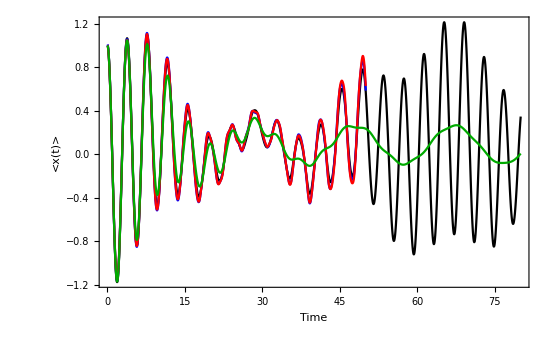

```mathematica
ListLinePlot[{dvrx[[1]],dhkx[[1]],hwdx[[1]],lscx[[1]]},PlotStyle->{Black,Blue,Red,Darker[Green]},PlotRange->Full,GridLines->None,FrameLabel->{"Time","<x(t)>"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],PlotRangePadding->0,BaseStyle->Directive[16,Black],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black]]
```

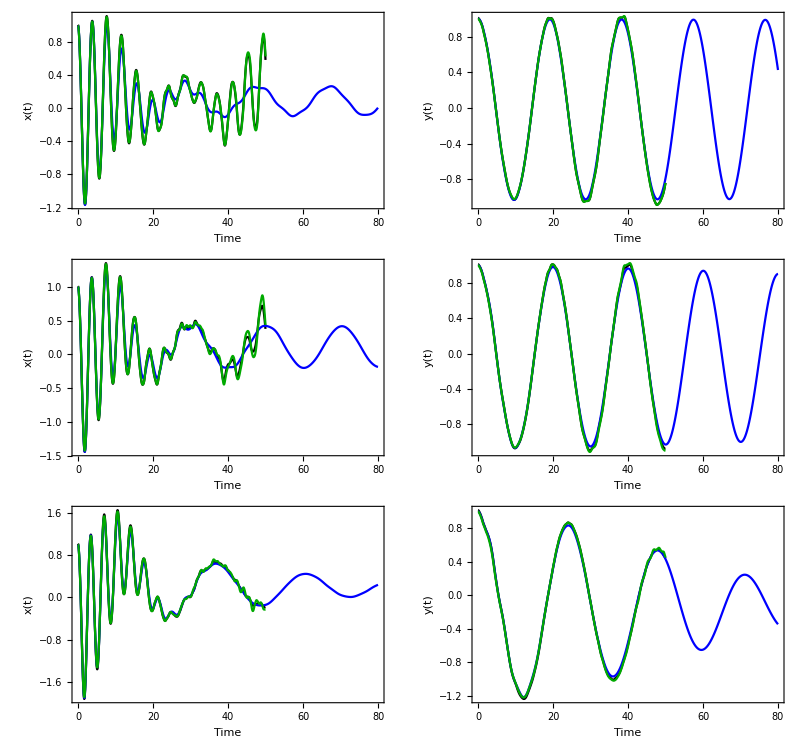

```mathematica
plot1=Legended[GraphicsGrid[Table[{ListLinePlot[{(*dvrx[[j]],*)dhkx[[j]],lscx[[j]],hwdx[[j]]},PlotStyle->{Black,(*Red,*)Blue,Darker[Green]},PlotRange->Full,GridLines->None,FrameLabel->{"Time","x(t)"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],PlotRangePadding->0,BaseStyle->Directive[16,Black],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black]],ListLinePlot[{(*dvry[[j]],*)dhky[[j]],lscy[[j]],hwdy[[j]]},PlotStyle->{Black,(*Red,*)Blue,Darker[Green]},PlotRange->Automatic,GridLines->None,FrameLabel->{"Time","y(t)"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],PlotRangePadding->0,BaseStyle->Directive[16,Black],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black]]},{j,1,3}],Spacings->0],Placed[LineLegend[{Black,(*Red,*)Blue,Darker[Green]},{(*"DVR",*)"DHK","LSC","HWD"},LegendLayout->"Row"],Top]]
```

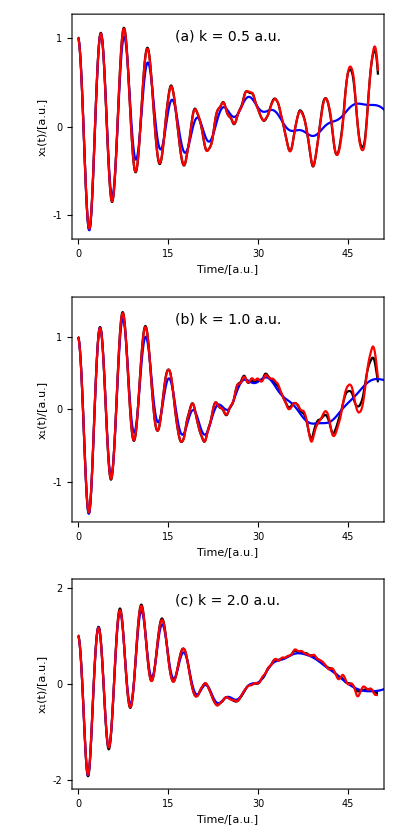

```mathematica
plot1=Legended[GraphicsColumn[{ListLinePlot[{dhkx[[1]],lscx[[1]],hwdx[[1]]},PlotStyle->{Black,Blue,Red},PlotRange->{{0,50},{-1.22,1.22}},GridLines->None,FrameLabel->{"Time/[a.u.]","x_1(t)/[a.u.]"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],BaseStyle->Directive[16,Black],FrameTicks->{{{-1,0,1,2},None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black],ImagePadding->{{Automatic, 5}, {60,Automatic}},Epilog->Text[Style["(a) k = 0.5 a.u.",14],Scaled[{0.5,0.90}]]],ListLinePlot[{dhkx[[2]],lscx[[2]],hwdx[[2]]},PlotStyle->{Black,Blue,Red},PlotRange->{{0,50},{-1.5,1.5}},GridLines->None,FrameLabel->{"Time/[a.u.]","x_1(t)/[a.u.]"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],BaseStyle->Directive[16,Black],FrameTicks->{{{-2,-1,0,1,2},None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black],ImagePadding->{{Automatic, 5}, {60,Automatic}},Epilog->Text[Style["(b) k = 1.0 a.u.",14],Scaled[{0.5,0.90}]]],ListLinePlot[{dhkx[[3]],lscx[[3]],hwdx[[3]]},PlotStyle->{Black,Blue,Red},PlotRange->{{0,50},{-2.1,2.1}},GridLines->None,FrameLabel->{"Time/[a.u.]","x_1(t)/[a.u.]"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],BaseStyle->Directive[16,Black],FrameTicks->{{{-4,-2,0,2,4},None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black],Epilog->Text[Style["(c) k = 2.0 a.u.",14],Scaled[{0.5,0.90}]]]},Spacings->0],Placed[LineLegend[{Black,Blue,Red},{"DHK","LSC","AHWD"},LegendLayout->"Row"],Top]]
```

```mathematica
Export["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\HHB\\not-normalized\\HHB.pdf",plot1]
```

C:\Users\shrey\Documents\Lab\SC-IVR Code\HHB\not-normalized\HHB.pdf